In the Mma string the backslash represents an escaped character.  Of course, an actual backslash is \\. I manually doubled all the backslashes in the latex code.  I could automate this using SED or some other tools.  An easy semi-automatic way to do it would be with a global find replace in a WYZWIF text editor.

\sum_{i=1}^4 \cos(i+x*\sin(i * x))

∑_(i=1)^4 Cos[i+x Sin[i x]]

Cos[1+x Sin[x]]+Cos[2+x Sin[2 x]]+Cos[3+x Sin[3 x]]+Cos[4+x Sin[4 x]]

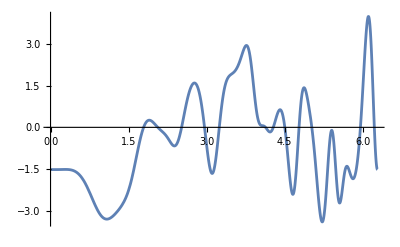

```mathematica
MyTest="\\sum_{i=1}^4 \\cos(i+x*\\sin(i * x))"
ToExpression[MyTest,TeXForm,HoldForm]
f[x_]=ToExpression[MyTest,TeXForm]
Plot[f[x],{x,0, 2π}]
```

```mathematica
"\\sum_{i=1}^4 \\cos(x*\\sin(i + x))"
```

\sum_{i=1}^4 \cos(x*\sin(i + x))

```mathematica
"\\sum_{i=1}^4 \\cos(x*\\sin(i*x))"
```

\sum_{i=1}^4 \cos(x*\sin(i*x))